```mathematica
SetDirectory["D:\\Utz\\Math_kurs\\Data"]
```

D:\Utz\Math_kurs\Data

```mathematica
FileNames["*.tsv"]
```

{Echo86.tsv,He_Xe_DataV1.tsv,He_Xe_DataV2.tsv,motorvehicle.tsv,U_I_Graphen.tsv}

```mathematica
data = Import["motorvehicle.tsv"][[3;;]];
```

```mathematica
Depth[data]
```

3

```mathematica
Dimensions[data]
```

{50,6}

```mathematica
Grid[data[[1;;8]],Frame -> All]
```

Alabama | 13. | s | 681. | 927. | 16.14
Alaska | 8. | s | 571. | 868. | 12.45
Arizona | 18. | s | 653. | 771. | 18.01
Arkansas | 18.7 | s | 732. | 616. | 13.22
California | 16. | s | 667. | 737. | 17.66
Colorado | 22. | s | 620. | 958. | 16.02
Connecticut | 26. | p | 674. | 798. | 17.68
Delaware | 19. | s | 728. | 790. | 16.97

```mathematica
beltuse = Tally[data[[All,3]]]
```

{{s,32},{p,9},{no,9}}

```mathematica
?BarChart
```

BarChart[{y_1,y_2,…}] makes a bar chart with bar lengths y_1,  y_2, ….
BarChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a bar chart with bar features defined by the symbolic wrappers w_k.
BarChart[{data_1,data_2,…}] makes a bar chart from multiple datasets data_i.

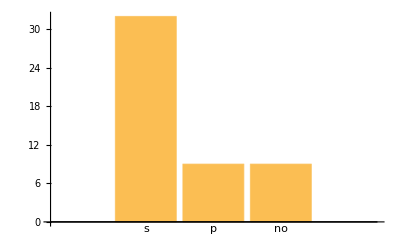

```mathematica
BarChart[beltuse[[All,2]],ChartLabels -> beltuse[[All,1]],BaseStyle -> {FontSize -> 18}]
```

```mathematica
PieChart[beltuse[[All,2]],ChartLabels -> beltuse[[All,1]],BaseStyle -> {FontSize -> 18}]
```

-Graphics-

```mathematica
PieChart3D[beltuse[[All,2]],ChartLabels -> beltuse[[All,1]],BaseStyle -> {FontSize -> 18}]
```

-Graphics3D-